# Physics 362 Cosmology Spring 2005

## Roger Blandford

#### Initialization

```mathematica
SetDirectory["/Users/rogerblandford/Desktop/teaching/ph362"];
```

SetDirectory::cdir: Cannot set current directory to /Users/rogerblandford/Desktop/teaching/ph362.

1. The Standard Model

## 1.1 Introduction

In these lectures,which follow Bob Wagoner's set, I will try to explain what we can learn about the Universe by studying the growth of perturbations.There are two major observational endeavors,strongly coupled-studying the perturbation spectrum in the ancient universe at the epoch of recombination using the microwave background and studying it in the contemporary and local universe though galaxy and cluster counts,gravitational lensing and the intergalactic medium.The progress over the past decade has been remarkable and we now have a standard model of the Universe.The current challenge is test it and/or go beyond it.Theoretically,the context of these investigations is to study dark energy and inflation which are two paths to enlightenment on fundamental physics.In these lectures,I would like explain what has been learned and to "deconstruct" the subject so as to try to develop a qualitative appreciation of the sensitivities in the problem.In truth,some of this is new to me and I so you must be vigilant!
My plan will be to set the stage-the "ΛCDM" model - describe the formalism for handling the growth of matter perturbations,  generalize this to discuss recombination and the connection to the early Universe and then look at future observational prospects, in particular with regard to studying dark energy using weak gravitational lensing. I will work in the linear and quasi-linear regime, leaving the discussion of the late time evolution of structure to the Fall 2005 class.

## 1.2 Matter-dominated era

### 1.1.1 ΛCDM

#### History

At the risk of getting a bit ahead of the observations, let me define the standard model as (flat) ΛCDM with scale invariant density fluctuations (n=1), and adopt the Pythagorean values h=Ω_Λ=2^(-1/2), Ω_b=0.04, Ω_γ=4.9 x 10^-5, Ω_ν=3.4 x 10^-5. I will also assume that all matter remains cold.  I will eschew redshift in favor of they scale factor a=(1+z)^-1, normalizing to unity, today. I see a as a good independent variable to use for these purposes, because we commonly measure the redshift and  the density of useful astronomical information per unit a, after recombination, is, roughly and subjectively, constant. As already discussed, a(t) satisfies
OverDot[a^2]=H_0^2[Ω_Λ a^2+(1-Ω_Λ)a^-1]
where the dot denotes differentiation with respect to cosmic time.  The solution, which was given by Bondi (1952) and almost given in 1927 by Lemaître, (he guessed that the universe was closed), is
a=(Ω_Λ^-1-1)^(1/3)sinh^(2/3)[(3 Ω_Λ^(1/2)H_0 t)/2].
This is not very new. Eddington (1935) strongly advocated this model on the (still pertinent) grounds that it could remove the disparity between the ages of the Universe and the stars and that it introduced a connection between the smallest and the largest scales (which is an inversion of the current statement of the problem!).

#### Jerk

This solution has the curious mathematical property that the jerk parameter,
j=((ä)^. a^2)/OverDot[a^3]=1.
This is the basis of a kinematic classification of world models.

### 1.1.2 Time, distance, volume

#### Parameters

It is helpful to gain some familiarity with the form and size of this variation. Let us measure time in Gyr, distances in Gpc. Then the Hubble distance is 4.23 and the Hubble time 13.8 and a=0.74 sinh^(2/3)(0.0915t). The critical density is 3H_0^2/8πG.

```mathematica
h=.71;Ω=.25;th=30.9/(3.15h)
dh=3./h
ρc=(27×10^20)/(8π 6.67×10^-8(3.15×10^16 th)^2)
```

13.8162

4.22535

8.5035×10^-9

#### Cosmic time

Inverting this we obtain the "spacetime" diagram
t(a)=10.9 arcsinh[1.56 a^(3/2)].

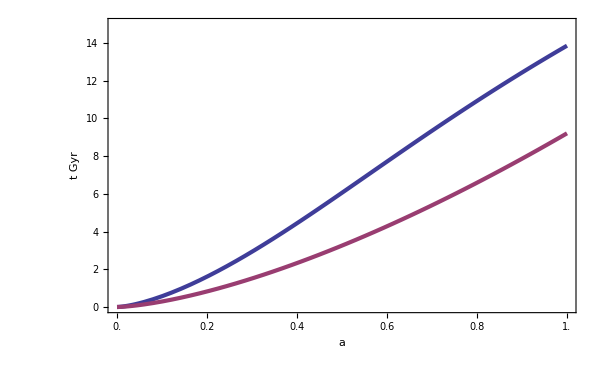

-Graphics-

-Graphics-

-Graphics-

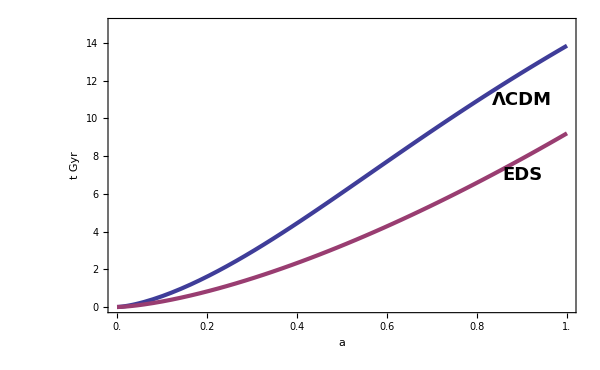

```mathematica
a[t_]:=(Ω/(1-Ω))^(1/3) Sinh[(1.5(1-Ω)^0.5 t)/th]^(2/3)
t[a_]:=(0.66667 th ArcSinh[((1-Ω)/Ω)^0.5 a^1.5])/(1-Ω)^0.5
teds[a_]:=0.66667 th a^1.5
tou[a_]:=th NIntegrate[1/(√(Ω/ap+(1-Ω))),{ap,0,a}]
tplt=Plot[{t[a],teds[a]},{a,0,1},Frame->True,PlotRange->{0,15},PlotStyle->Thickness[0.005],FrameLabel->{Style["a",FontFamily->"Courier",FontSize->16,FontWeight->"Bold"],Style["t Gyr",FontFamily->"Courier",FontSize->16,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->16,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Table[{a,Style[a,FontFamily->"Courier",FontSize->16,FontWeight->"Bold"]},{a,0,1,0.2}],Table[{t,Style[t,FontFamily->"Courier",FontSize->16,FontWeight->"Bold"]},{t,0,14,2}],Table[{1/(1+z),Style[z,FontFamily->"Courier",FontSize->16,FontWeight->"Bold"]},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->Identity]
labelΛCDM=Graphics[Text[Style["ΛCDM",FontFamily->"Courier",FontSize->18,FontWeight->"Bold"],{0.9,11}]]
labeleds=Graphics[Text[Style["EDS",FontFamily->"Courier",FontSize->18,FontWeight->"Bold"],{0.9,7}]]
labelou=Graphics[Text[Style["OU",FontFamily->"Courier",FontSize->18,FontWeight->"Bold"],{0.9,9}]]
taplt=Show[tplt,labelΛCDM,labeleds,DisplayFunction->$DisplayFunction]
Export["taplt.jpg",taplt];
```

```mathematica
t[a]/.a->1/11
```

0.49496

```mathematica
t[1/(1+10)]/.45
(6.65 10^-25 3 10^10)/(4π 6.67 10^-8 1.67 10^-24 3.15 10^7)
```

1.09991

4.5246×10^8

Note that t[1]=13.7. For comparison, we show an Einstein-De Sitter model with the same H_0 and an open universe model with the same H_0, Ω_m.

```mathematica
1.5 10^-4 10^46 3.1 10^16 8.2/(1.8 10^20 2 10^41 5)
```

0.00211833

#### Conformal time

We also need the conformal time defined by
η(t)=(∫_0)^tdt'/a(t') 
in terms of which the metric becomes Minkowskian times (a(t))^2 so that null geodesics are unchanged.

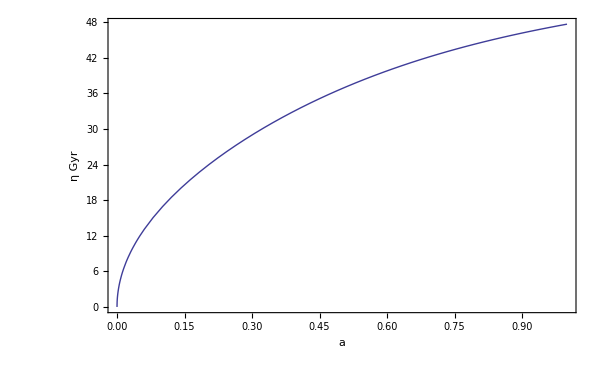

```mathematica
η[a_]:=(th Beta[((1-Ω) a^3)/(Ω+(1-Ω) a^3),1/6,1/3])/(3 Ω^(1/3) (1-Ω)^(1/6))
ηplt=Plot[η[a],{a,0,1},Frame->True,PlotRange->{0,η[1]},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["η Gyr",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->$DisplayFunction]
```

The universe is much older in terms of conformal time.

#### Affine time

A third useful time measure which we will use later is the affine time which comes from solving
dx^α/dλ=k^α/ω(1)
or
λ(t)=(∫_0)^tdt'a(t')

```mathematica
NIntegrate[ap/(√((1-.26) ap^2+(.26)/ap)),{ap,.418,.614}]/.614
```

0.195787

```mathematica
.4632 .3430 .614/.1202
```

0.811571

```mathematica
0.8115711014975042/.737
```

1.10118

```mathematica
nds=NDSolve[{(.26 a^2+(1-.26)a^5)ξp'[a]-(3 .26 a)/2 ξp[a]+(3 .26 0)/2 ξ[a]==0,ξ'[a]==ξp[a],ξp[.6135]==-(.26/.6135+.74 (.6135)^2)^(-.5),ξ[.6135]==0},{ξ,ξp},{a,.6135,.4177}][[1]];
ξ[.4177]/.nds
```

0.195586

```mathematica
.418.335/.190
```

0.737

```mathematica
1.32/.737
```

1.79104

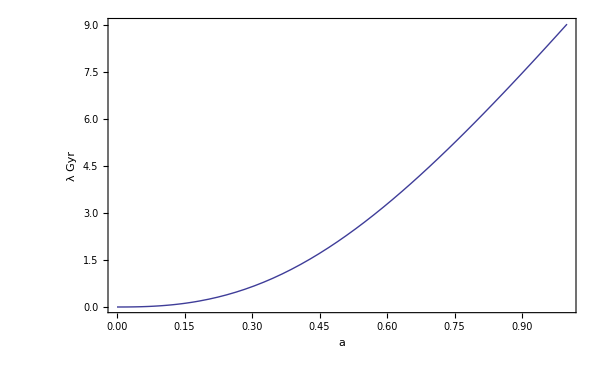

```mathematica
λ[a_]:=th NIntegrate[ap/(√((1-Ω) ap^2+Ω/ap)),{ap,0,a}];λplt=Plot[λ[a],{a,0,1},Frame->True,PlotRange->{0,λ[1]},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["λ Gyr",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->$DisplayFunction]
```

The Universe is much younger in terms of affine time.

#### Distance

The (co-moving) distance out to a source in a flat universe is given by
d(a)=c[η(1)-η(a)].
The angular diameter distance is d_A=a d, the luminosity distance d_L=a^-1 d.

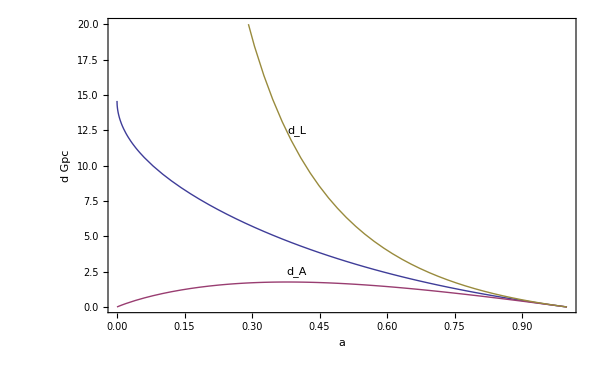

```mathematica
d[a_]:=(dh (η[1]-η[a]))/th
da[a_]:=a d[a]
dl[a_]:=d[a]/a
dplt=Plot[{d[a],da[a],dl[a]},{a,0,1},Frame->True,PlotRange->{0,20},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["d Gpc",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->Identity];
labelda=Graphics[Text["\!\(\*SubscriptBox[\(d\), \(A\)]\)",{0.4,2.5}]];
labeldl=Graphics[Text["\!\(\*SubscriptBox[\(d\), \(L\)]\)",{0.4,12.5}]];
Show[dplt,labelda,labeldl,DisplayFunction->$DisplayFunction]
```

```mathematica
d[1/1.8]
1/.65
```

2.79346

1.53846

```mathematica
10^6 da[1/6]π/(180 3600)
```

6.40474

```mathematica
16. 10^5/3600^2
```

0.123457

```mathematica
12 .02 (.4)^2
```

0.0384

```mathematica
Log[10,(3.6 10^(-9-12)6060 4π (3.09 10^27 dl[a])^2)/(3.9 10^33)]/.a->1/(1+1)
```

7.46444

The distance to the early universe is 14.2 Gpc. (Actually this has to be corrected for radiation. We will deal with this later.)
Note that the angular diameter distance has a maximum (at a=0.38), and the luminosity distance diverges.

#### Distance Modulus

It is instructive to plot this in terms of the astronomical quantity, the distance modulus
m-M=5 log_10[d_L/10pc]

-Graphics-

-Graphics-

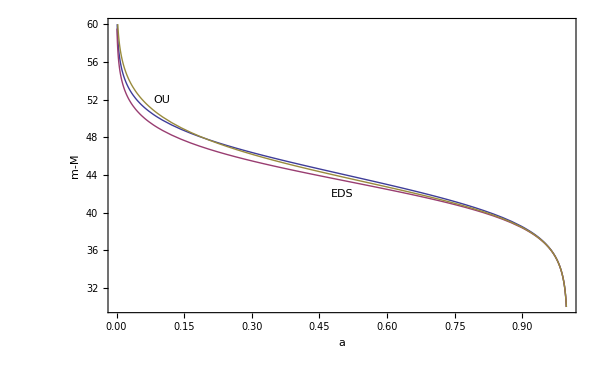

```mathematica
mm[a_]:=40+5 Log[10,dl[a]]
mattig[Ω_,a_]:=(2 dh (Ω z-(2-Ω) (√(1+Ω z)-1)))/Ω^2/.z->1/a-1
mmeds[a_]:=40+5 Log[10,mattig[1,a]]
mmou[a_]:=40+5 Log[10,mattig[Ω,a]]
mmplt=Plot[{mm[a],mmeds[a],mmou[a]},{a,0.001,0.999},Frame->True,PlotRange->{30,60},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["m-M",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->Identity];
labelmmeds=Graphics[Text["EDS",{0.5,42}]]
labelmmou=Graphics[Text["OU",{0.1,52}]]
Show[mmplt,labelmmeds,labelmmou,DisplayFunction->$DisplayFunction]
```

Note that the distance moduli for these three models at a=0.5 are 44.1, 43.5 and 43.8 respectively and very accurate measurements would be needed to test the standard model using direct distance measurement. However, this may not the best way to think about the problem.  We may know the distance to the early universe from the microwave background. In our three models, this is d(0)= 14, 8.4, 29 respectively suggesting that the best kinematic approach to testing the standard model will come from knowing H_0,Ω_m,d(0) together .

#### Volume

Finally, we plot the growth of (co-moving) volume out to a.
V=(4 πd^3)/3

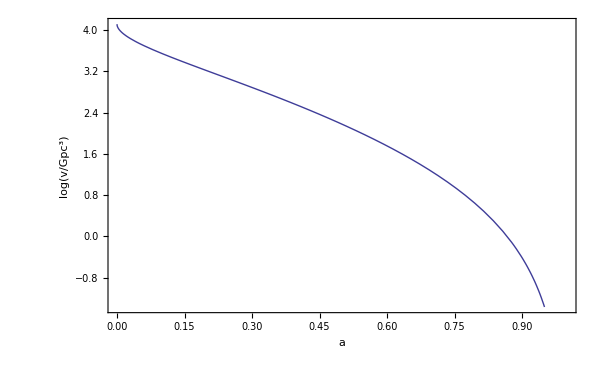

```mathematica
v[a_]:=1/3 (4 π) d[a]^3
vplt=Plot[Log[10,v[a]],{a,0,1},Frame->True,PlotRange->{Log[10,v[0.95]],Log[10,v[0]]},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["log(v/\!\(\*SuperscriptBox[\(Gpc\), \(3\)]\))",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->Identity];
Show[vplt,DisplayFunction->$DisplayFunction]
```

Note that the comoving volume to a=0 is 1.3 x 10^4, 80 times that to a=0.5.

```mathematica
v[0]
```

13015.2

## 1.3 Radiation

### 1.3.1 Parameters

We include radiation including photons (Ω_γ) and neutrinos (Ω_ν). a_eq=Ω_r/Ω=0.00029is the epoch of matter-radiation (including neutrinos) equality. The recombination temperature, (see below) is T_rec=3000 K, so the epoch of recombination is a_rec = 2.73/2970=0.00092.

```mathematica
Ωb=0.04;Ωd=Ω-Ωb;Ωγ=0.000049;Ων=0.000034;Ωr=Ωγ+Ων;aeq=Ωr/Ω
arec=0.00092
tγ=2.73
```

0.000319231

0.00092

2.73

### 1.3.2 Expansion rate

The modified expansion is governed by the equation
OverDot[a^2]=H_0^2[Ω_Λ a^2+(1-Ω_Λ-Ω_r)a^-1+Ω_r a^-2]
so that

```mathematica
tr[a_]:=th NIntegrate[1/(√(Ω/ap+(1-Ω-Ωr) ap^2+Ωr/ap^2)),{ap,0,a}]
```

```mathematica
tr[.09]
```

0.485162

```mathematica
trplt=Plot[{tr[a],t[a]},{a,0,0.003},Frame->True,PlotRange->{0,tr[0.003]},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["t Gyr",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,FrameTicks->{Automatic,Automatic},ImageSize->600,DisplayFunction->Identity];
recline=Graphics[Line[{{arec,0},{arec,tr[0.003]}}]]
eqline=Graphics[Line[{{aeq,0},{aeq,tr[0.003]}}]]
labelrad=Graphics[Text["Radiation + Matter",{0.0022,0.001}]];labelmat=Graphics[Text["Matter",{0.0022,0.002}]];labelrec=Graphics[Text["Recombination",{0.0012,0.002}]]
labeleq=Graphics[Text["Equality",{0.00045,0.002}]]
Show[trplt,recline,eqline,labelrad,labelmat,labelrec,labeleq,DisplayFunction->$DisplayFunction]
```

### 1.3.3 Horizon

The comoving particle horizon size is given by the conformal time

```mathematica
ηr[a_]:=th NIntegrate[(1/(√(Ω/ap+(1-Ω-Ωr) ap^2+Ωr/ap^2)))/ap,{ap,0,a}]
horizplt=Plot[{(dh ηr[a])/th},{a,0,0.003},Frame->True,PlotRange->{0,(dh ηr[0.003])/th},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["Horizon Gpc",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],"",Style["θ deg",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,FrameTicks->{Automatic,Automatic,Automatic,Table[{(13.6 π θ)/180,θ},{θ,1,2}]},ImageSize->600,DisplayFunction->Identity];
linerec=Graphics[Line[{{arec,0},{arec,3}}]]
labelrec=Graphics[Text["Recombination",{0.0012,0.6}]]
Show[horizplt,linerec,labelrec,DisplayFunction->$DisplayFunction]
drplt=Plot[{(dh (ηr[1]-ηr[a]))/th,d[a]},{a,0,0.003},Frame->True,PlotRange->{12,15},PlotStyle->{{Thickness[0.003]},{Dashing[{0.01}]}},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["d Gpc",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
linerec=Graphics[Line[{{arec,12},{arec,15}}]]
lineeq=Graphics[Line[{{aeq,12},{aeq,15}}]]
labelrec=Graphics[Text["Recombination",{0.0012,14.5}]]
labeleq=Graphics[Text["Equality",{0.00045,14.5}]]
Show[drplt,linerec,lineeq,labelrec,labeleq,DisplayFunction->$DisplayFunction]
```

Horizon  size in comoving Mpc. The distance to recombination is 13.6 and the angular size of the horizon is shown in degrees.

```mathematica
(ηr[1]-ηr[.00092])dh/th
```

General::obspkg: "Graphics`Graphics`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::newpkg: "Graphics`PlotField`" is now available as the "Vector Field Plot Package". See the Compatibility Guide for updating information.

General::obspkg: "Graphics`Arrow`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::newpkg: "Graphics`Polyhedra`" is now available as the "Polyhedron Operations Package". See the Compatibility Guide for updating information.

Triangle::shdw: Symbol "Triangle" appears in multiple contexts {"Geometry`Polytopes`", "Graphics`MultipleListPlot`"}; definitions in context "Geometry`Polytopes`" may shadow or be shadowed by other definitions.

General::newpkg: "Graphics`PlotField3D`" is now available as the "Vector Field Plot Package". See the Compatibility Guide for updating information.

General::stop: Further output of General :: "newpkg" will be suppressed during this calculation.

General::obspkg: "Graphics`Graphics3D`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

General::stop: Further output of General :: "obspkg" will be suppressed during this calculation.

2. Linear Growth of Structure

## 2.1 Newtonian Growth of Matter Perturbations

### 2.1.1 History

It is appropriate to call this Newtonian growth because Newton actually thought about this problem and appreciated that gravitational attraction caused matter to agglomerate. He also tried to explain sound waves, but did not understand the difference between adiabatic and isothermal perturbations. This had to await Laplace. Jeans (1902) explained the exponential growth of perturbations in a static universe. In the context of relativistic cosmology, Lemaître (1929) had a pretty good understanding of the problem, but the first correct description of power law growth in an expanding universe was given by Lifshitz (1946).

### 2.1.2 Sound waves

#### Fluid Model

Let us treat the contents of the Universe on the large scale as an isotropic, Newtonian fluid endowed with pressure, density and velocity. In the continuum approximation, the equations of continuity and motion  in a uniform and stationary background are:
∂_t ρ+∇·ρ v=0
∂_t v+v·∇v=-∇P/ρ.
Considering linear perturbations and introducing the notation δ≡δρ/ρ, which is only mildly confusing, we obtain:
∂_t δ+∇·v=0
∂_t v=-s^2∇δ,
where v is a perturbation and s^2=dP/dρ is the sound speed. s must be interpreted very carefully. It is the response of the fluid to small changes on a specific temporal and spatial scale. For a perfect gas, s^2=γP/ρ. For interstellar gas subject to astrophysical heating and cooling and thermostated to 10^4 K, it will be P/ρ. s=0 for cold dark matter.

#### Sound waves

Combining these two equations, we obtain the wave equation:
δ̈=s^2∇^2 δ,
with the dispersion relation
ω^2=s^2 k^2.

### 2.1.3 Jeans' instability

#### Gravity

Now add Newtonian gravity as a perturbation.
∇·g=-4πGρδ
∇×g=0

#### Perturbed equations

Again we ignore it in the equilibrium state and so g must be added to the rhs of the perturbed equation of motion. The perturbation equation becomes
δ̈=s^2(∇^2 δ+k_J^2 δ),
where 
k_J=(4πGρ)^(1/2)/s
is the Jeans' wave number. The associated Jeans' length is 
λ_J=2π/k_J=(s(π/Gρ))^(1/2)=2(s/(10 km s^-1))(ρ/(10^-24 g cm^-3))^(-1/2)kpc
There is a Jeans' mass, variously defined
M_J=ρλ_J^3=10^8(s/(10 km s^-1))^3(ρ/(10^-24 g cm^-3))^(-1/2)M_⊙
The dispersion relation is
ω^2=s^2(k^2-k_J^2)
and the growth is exponential for wavelengths longer than the Jeans' length. This is like a plasma oscillation except that the force is attractive!

Perturbations below the Jeans' scale will not grow but simply oscillate. For larger perturbations, the collapse time ~ (Gρ)^(-1/2)is shorter than the time it takes a compression wave to cross the scale. The Jeans' criterion is crucial to the growth of pre-galactic perturbations in the early universe as a typical perturbation falls successively above, below and above the Jeans' scale while the universe expands.

### 2.1.4 Expanding universe

#### Hubble expansion

Expand about the origin and assume the Hubble law for the background flow.
V=H(t) a(t) x=ȧx
where H=ȧ/a, and x is a comoving coordinate. Henceforth, all spatial derivatives are taken with respect to comoving coordinates. Mass conservation in the background flow implies that 
ρ̇+3ρH=0

#### Perturbation equation of continuity

OverDot[(ρδ)]+(ρ∇·v)/a+3Hρδ=0
⇒δ̇+(∇·v)/a=0

#### Perturbed equation of motion

v̇+Hv=-(s^2∇δ)/a-(∇ϕ)/a
where ϕ is the Newtonian potential and we have written the pressure perturbation as ρ δ s^2.

#### Poisson's equation

∇^2 ϕ=4 πGρδa^2

#### Transverse Mode

The equation of continuity has solutions satisfying
OverDot[v_⊥]+Hv_⊥=0
with v_⊥∝a^-1. These decay and can be ignored. These modes have vorticity and are incompressible.

#### Longitudinal Mode

Combine equations to obtain
OverDot[(a δ̇)]+Ha δ̇-(s^2∇^2 δ)/a-4πGρaδ=0
⇒δ̈+2Hδ̇-(s^2∇^2 δ)/a^2-4πGρδ=0
The Jeans' equation is supplemented by a friction term which takes account of the expansion of the universe.

#### Einstein-De Sitter

Ignore the pressure term when the matter is cold
H=2/(3t), 4πGρ=2/(3 t^2). Let δ∝ t^n. 
n^2+n/3-2/3=0  or  n=2/3,-1. 
Generically, there is a growing and a decaying mode. We are interested in the former. In this case, δ∝a and δϕ, the perturbed Newtonian potential, is constant. This is valid in the early, matter-dominated universe,

#### DeSitter

δ̈+2H δ̇=0⇒δ∝const or a^-2. For the growing mode the potential decays ∝a^-1. This will be appropriate in our future (we think!).

### 2.1.5 Heuristic treatment

#### Spherical Perturbation

Some insight comes from considering a spherical, positive density perturbation expanding at early time within a uniform expanding background.

#### Einstein-De Sitter

For a flat EDS background, the perturbation will have positive spatial curvature and behave like a closed universe. It will reach maximum expansion and re-collapse. Without loss of generality, we can choose our units so that 
(ȧ)^2=a^-1-1
which has parametric solution
a=sin^2 χ
t=χ-sinχcosχ
so that turnaround occurs at χ=π/2.
The background expands according to 
a=(3t/2)^(2/3)which matches the closed universe at early times. Taylor expanding for early time,
t=2/3 χ^3+…
a=χ^2(1-χ^2/3+…). Hence
(δa/a)_EDS=-a/3+…
and the density perturbation grown according to δ=a+… in these units. 
At maximum expansion, t=π/2 and
δ=(a_EDS/a)^3=9π^2/16=5.5
a will subsequently decrease to zero when χ=π. In reality, perturbations will be non-spherical and inhomogeneous and there will be shocks, violent relaxation, shell crossings etc after the radius of the sphere has roughly halved so that χ~3π/4, t~3π/4+1/2, δ~150. There will be virialization at this radius.
If the perturbation is  an underdense sphere, a spherical compression wave will be driven into the background medium.

#### ΛCDM

More usefully, repeat this exercise for a ΛCDM cosmology, We again choose units so that
OverDot[a^2]=4/9(a^-1+a^2-k)
The unperturbed solution with k=0 is a =sinh^(2/3)t with t=1.23 now. The rhs has a negative minimum, corresponding to turnaround, if k>2^(-2/3)+2^(1/3)=1.89. The perturbed differential equation has a solution in terms of elliptic functions, but it is easier to proceed numerically.

```mathematica
a1=0.00001;t1=ArcSinh[a1^1.5];ar=0.00092;tr=ArcSinh[ar^1.5];nds0=NDSolve[{a'[t]==0.6667 √(1/a[t]+a[t]^2),a[t1]==a1},a,{t,t1,2}];
plt0=Plot[a[t]/.nds0,{t,tr,2},Frame->True,PlotRange->{0,3},FrameLabel->{Style["t",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
nds1=NDSolve[{a'[t]==0.6667 √(1/a[t]+a[t]^2-1),a[t1]==a1},a,{t,tr,2}];
plt1=Plot[a[t]/.nds1,{t,tr,2},Frame->True,PlotRange->{0,3},FrameLabel->{Style["t",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
nds2=NDSolve[{a'[t]==0.6667 √(1/a[t]+a[t]^2-1.889),a[tr]==ar},a,{t,tr,2}];
plt2=Plot[a[t]/.nds2,{t,tr,2},Frame->True,PlotRange->{0,3},FrameLabel->{Style["t",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
t1=0.001;
a1=a[0.001]/.nds1⟦1⟧
a2=a[0.001]/.nds2⟦1⟧
δ2=(1-a2/a1)^3
δr=(δ2 ar)/a2
nds3=NDSolve[{a'[t]==0.6667 √(1/a[t]+a[t]^2-1.93),a[1.*^-6]==0.00015^0.667},a,{t,1.*^-6,1.22}];
plt3=Plot[a[t]/.nds3,{t,1.*^-6,1.22},Frame->True,PlotRange->{0,3},FrameLabel->{Style["t",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
nds4=NDSolve[{a'[t]==-0.6667 √(1/a[t]+a[t]^2-1.93),a[1.23]==a4},a,{t,1.24,2}];
plt4=Plot[a[t]/.nds4,{t,1.24,2},Frame->True,PlotRange->{0,3},FrameLabel->{Style["t",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
Show[{plt0,plt1,plt2},DisplayFunction->$DisplayFunction]
```

0.00998038

0.0099626

5.65416×10^-9

5.22136×10^-10

We see that universes with k<1.89 do not turn around but follow the ΛCDM univere into exponential expansion. The associated overdensity at recombination of the marginal universe is δ=1.2×10^-7. A universe with k>1.89 will undergo a delayed collapse. A universe with k=1.93 turns around today.

### 2.1.6 Growth of small scale matter perturbations

#### Density

We rewrite the perturbation for normal modes with a as the independent variable.
([a^2{Ω_Λ a^2+(1-Ω_Λ)/a})^(1/2)δ']'-(3(1-Ω_Λ)δ)/(2{Ω_Λ a^2+(1-Ω_Λ)/a}^(1/2))=0
A prime denotes differentiation with respect to a. 
Equivalently,
{Ω_Λ a^2+(1-Ω_Λ)/a}δ''+{3Ω_Λ a+(3(1-Ω_Λ))/(2 a^2)}δ'-(3(1-Ω_Λ)δ)/(2 a^3)=0

```mathematica
nds=NDSolve[{((1-Ω) a^2+Ω/a) δ''[a]+(3 (1-Ω) a+(3 Ω)/(2 a^2)) δ'[a]-(3 Ω δ[a])/(2 a^3)==0,δ[arec]==1,δ'[arec]==1/arec},δ[a],{a,arec,1}];
δplt=Plot[{δ[a]/.nds,a/arec},{a,arec,1},Frame->True,PlotRange->{0,1000},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["δ",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->Identity];
labelΛCDM=Graphics[Text["ΛCDM",{0.7,600}]]
labeleds=Graphics[Text["EDS",{0.7,800}]]
Show[δplt,labelΛCDM,labeleds,DisplayFunction->$DisplayFunction]
```

#### Velocity

We showed that 
v=i OverDot[δa]/k=i H_0/k{Ω_Λ a^2+(1-Ω_Λ)/a}^(1/2)aδ'
A well known approximation is 
a δ'=Ω^0.6 δ.

```mathematica
del[a_]:=Evaluate[δ[a]/.nds⟦1⟧]
v[a_]:=√((1-Ω) a^2+Ω/a) a del'[a]
vplt=Plot[{v[a],(√Ω √a)/arec},{a,arec,1},Frame->True,PlotRange->{0,600},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["-\!\(\*FractionBox[\(ikv\), SubscriptBox[\(H\), \(0\)]]\)",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->Identity];
labelΛCDM=Graphics[Text["ΛCDM",{0.7,400}]]
labeleds=Graphics[Text["EDS",{0.7,500}]]
Show[vplt,labelΛCDM,labeleds,DisplayFunction->$DisplayFunction]
```

#### Potential

If we let the potential perturbation be ϕ, then 
ϕ=-(4 πGρa^2 δ)/k^2=-(3 ΩH_0^2 δ)/(2 ak^2)

```mathematica
ϕplt=Plot[{(3 Ω δ[a])/(2 a)/.nds,(3 Ω)/(2 arec)},{a,arec,1},Frame->True,PlotRange->{0,600},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["\!\(\*FractionBox[SuperscriptBox[\(ϕk\), \(2\)], SuperscriptBox[SubscriptBox[\(H\), \(0\)], \(2\)]]\)",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],""},RotateLabel->False,FrameTicks->{Automatic,Automatic,Table[{1/(1+z),z},{z,0,6}],Automatic},ImageSize->600,DisplayFunction->Identity];
labelΛCDM=Graphics[Text["ΛCDM",{0.7,400}]]
labeleds=Graphics[Text["EDS",{0.7,500}]]
Show[ϕplt,labelΛCDM,labeleds,DisplayFunction->$DisplayFunction]
```

This difference forms the basis of the Integrated Sachs-Wolfe effect.

## 2.2 Radiation Era

### 2.2.1 Physical Conditions

The dark matter and baryon densities (in units of erg cm^-3) plus the radiation pressure P are  given by:
ρ_d=(3H_0^2(Ω-Ω_b))/(8 πGa^3), 
ρ_b=(3 H_0^2 Ω_b)/(8 πGa^3), 
P=aT^4/(3 c^2 a^4)

```mathematica
ρd[a_]:=(Ωd ρc)/a^3;ρb[a_]:=(Ωb ρc)/a^3;pγ[a_]:=(Ωγ ρc)/(3 a^4);
ρplt=ParametricPlot[{{Log[10,a],Log[10,ρd[a]]},{Log[10,a],Log[10,ρb[a]]},{Log[10,a],Log[10,pγ[a]]}},{a,1/10^6,arec},Frame->True,PlotRange->{{-5,-3},{-1,7}},FrameLabel->{Style["Log[a]",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["Log[ρ(erg \!\(\*SuperscriptBox[\(cm\), \(-3\)]\))]",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
eqline=Graphics[Line[{{Log[10,aeq],-1},{Log[10,aeq],7}}]]
labeldar=Graphics[Text[Style["\!\(\*SubscriptBox[\(ρ\), \(d\)]\)",FontSize->14],{-3.25,2}]]
labelbar=Graphics[Text[Style["\!\(\*SubscriptBox[\(ρ\), \(b\)]\)",FontSize->14],{-4.5,3.5}]]
labelrad=Graphics[Text[Style["\!\(\*SubscriptBox[\(P\), \(γ\)]\)",FontSize->14],{-4.5,6}]]
labeleq=Graphics[Text[Style["\!\(\*SubscriptBox[\(a\), \(eq\)]\)",FontSize->14],{-3.48,5}]]
Show[ρplt,eqline,labeldar,labelbar,labelrad,labeleq,DisplayFunction->$DisplayFunction]
```

## 2.2 Relativistic Growth of Perturbations

We wish to consider the growth of perturbations at early times when the equation of state is relativistic and on scales large compared with the size of the horizon. The problem is unavoidably genereal relativistic.

### 2.2.3 Einstein Field Equations

We work in the Newtonian gauge in which 
ds^2=-(1+2ϕ)dt^2+a^2(1-2ψ)dx_i dx^i
Compute the mixed components of the Einstein tensor using
(Γ^α)_βγ=1/2 g^αδ(g_(δβ,γ)+g_(δγ,β)-g_(βγ,δ))
R_αβ=(Γ^γ)_(αβ,γ)-(Γ^γ)_(αγ,β)+(Γ^γ)_δγ(Γ^δ)_αβ-(Γ^γ)_δβ(Γ^δ)_αγ
(G^α)_β=(R^α)_β-1/2(Rδ^α)_β

```mathematica
coord={t,x,y,z};
metric={{-(1+2ϵ ϕ[t,x,y,z]),0,0,0},{0,(1-2ϵ ψ[t,x,y,z])a[t]^2,0,0},{0,0,(1-2 ϵ ψ[t,x,y,z])a[t]^2,0},{0,0,0,(1-2ϵ  ψ[t,x,y,z])a[t]^2}};
inversemetric:=inversemetric=Simplify[Inverse[metric]];
affine:=affine=Simplify[
Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coord[[k]] ]+
D[metric[[s,k]],coord[[j]] ]-D[metric[[j,k]],coord[[s]] ]),{s,1,4}],
{i,1,4},{j,1,4},{k,1,4}] ];
riemann:=riemann=
Simplify[Table[D[affine[[i,j,l]],coord[[k]]]-D[affine[[i,j,k]],coord[[l]]]+Sum[affine[[i,s,k]]*affine[[s,j,l]]-affine[[i,s,l]]affine[[s,j,k]],{s,1,4}],{i,1,4},{j,1,4},{k,1,4},{l,1,4}]]
riccitensor=Simplify[Table[Sum[riemann[[k,i,k,j]],{k,1,4}],{i,1,4},{j,1,4}]];
ricciscalar=Simplify[Sum[inversemetric[[i,j]]riccitensor [[j,i]],{i,1,4},{j,1,4}]];
einsteintensor=Series[Simplify[Table[Sum[inversemetric[[i,k]]riccitensor[[k,j]],{k,1,4}]-1/2 ricciscalar KroneckerDelta[i,j],{i,1,4},{j,1,4}]],{ϵ,0,1}];
deinstein=Table[SeriesCoefficient[einsteintensor[[i,j]],1],{i,1,4},{j,1,4}]
```

{{(6 ϕ[t,x,y,z] a'[t]^2)/a[t]^2-(2 ψ^(0,0,0,2)[t,x,y,z])/a[t]^2-(2 ψ^(0,0,2,0)[t,x,y,z])/a[t]^2-(2 ψ^(0,2,0,0)[t,x,y,z])/a[t]^2+(6 a'[t] ψ^(1,0,0,0)[t,x,y,z])/a[t],-(2 a'[t] ϕ^(0,1,0,0)[t,x,y,z])/a[t]-2 ψ^(1,1,0,0)[t,x,y,z],-(2 a'[t] ϕ^(0,0,1,0)[t,x,y,z])/a[t]-2 ψ^(1,0,1,0)[t,x,y,z],-(2 a'[t] ϕ^(0,0,0,1)[t,x,y,z])/a[t]-2 ψ^(1,0,0,1)[t,x,y,z]},{(2 a'[t] ϕ^(0,1,0,0)[t,x,y,z])/a[t]^3+(2 ψ^(1,1,0,0)[t,x,y,z])/a[t]^2,(2 ϕ[t,x,y,z] a'[t]^2)/a[t]^2+(4 ϕ[t,x,y,z] a''[t])/a[t]+(ϕ^(0,0,0,2)[t,x,y,z])/a[t]^2-(ψ^(0,0,0,2)[t,x,y,z])/a[t]^2+(ϕ^(0,0,2,0)[t,x,y,z])/a[t]^2-(ψ^(0,0,2,0)[t,x,y,z])/a[t]^2+(2 a'[t] ϕ^(1,0,0,0)[t,x,y,z])/a[t]+(6 a'[t] ψ^(1,0,0,0)[t,x,y,z])/a[t]+2 ψ^(2,0,0,0)[t,x,y,z],-(ϕ^(0,1,1,0)[t,x,y,z])/a[t]^2+(ψ^(0,1,1,0)[t,x,y,z])/a[t]^2,-(ϕ^(0,1,0,1)[t,x,y,z])/a[t]^2+(ψ^(0,1,0,1)[t,x,y,z])/a[t]^2},{(2 a'[t] ϕ^(0,0,1,0)[t,x,y,z])/a[t]^3+(2 ψ^(1,0,1,0)[t,x,y,z])/a[t]^2,-(ϕ^(0,1,1,0)[t,x,y,z])/a[t]^2+(ψ^(0,1,1,0)[t,x,y,z])/a[t]^2,(2 ϕ[t,x,y,z] a'[t]^2)/a[t]^2+(4 ϕ[t,x,y,z] a''[t])/a[t]+(ϕ^(0,0,0,2)[t,x,y,z])/a[t]^2-(ψ^(0,0,0,2)[t,x,y,z])/a[t]^2+(ϕ^(0,2,0,0)[t,x,y,z])/a[t]^2-(ψ^(0,2,0,0)[t,x,y,z])/a[t]^2+(2 a'[t] ϕ^(1,0,0,0)[t,x,y,z])/a[t]+(6 a'[t] ψ^(1,0,0,0)[t,x,y,z])/a[t]+2 ψ^(2,0,0,0)[t,x,y,z],-(ϕ^(0,0,1,1)[t,x,y,z])/a[t]^2+(ψ^(0,0,1,1)[t,x,y,z])/a[t]^2},{(2 a'[t] ϕ^(0,0,0,1)[t,x,y,z])/a[t]^3+(2 ψ^(1,0,0,1)[t,x,y,z])/a[t]^2,-(ϕ^(0,1,0,1)[t,x,y,z])/a[t]^2+(ψ^(0,1,0,1)[t,x,y,z])/a[t]^2,-(ϕ^(0,0,1,1)[t,x,y,z])/a[t]^2+(ψ^(0,0,1,1)[t,x,y,z])/a[t]^2,(2 ϕ[t,x,y,z] a'[t]^2)/a[t]^2+(4 ϕ[t,x,y,z] a''[t])/a[t]+(ϕ^(0,0,2,0)[t,x,y,z])/a[t]^2-(ψ^(0,0,2,0)[t,x,y,z])/a[t]^2+(ϕ^(0,2,0,0)[t,x,y,z])/a[t]^2-(ψ^(0,2,0,0)[t,x,y,z])/a[t]^2+(2 a'[t] ϕ^(1,0,0,0)[t,x,y,z])/a[t]+(6 a'[t] ψ^(1,0,0,0)[t,x,y,z])/a[t]+2 ψ^(2,0,0,0)[t,x,y,z]}}

Now read off the trace free part of the spatial part of the metric

```mathematica
treinstein=Simplify[deinstein[[2,2]]+deinstein[[3,3]]+deinstein[[4,4]]]
Simplify[Table[deinstein[[i,j]]-If[i==j,treinstein,0]/3,{i,2,4},{j,2,4}]]
treinstein/6
```

1/a[t]^2(2 (3 ϕ[t,x,y,z] (a'[t]^2+2 a[t] a''[t])+ϕ^(0,0,0,2)[t,x,y,z]-ψ^(0,0,0,2)[t,x,y,z]+ϕ^(0,0,2,0)[t,x,y,z]-ψ^(0,0,2,0)[t,x,y,z]+ϕ^(0,2,0,0)[t,x,y,z]-ψ^(0,2,0,0)[t,x,y,z]+3 a[t] a'[t] ϕ^(1,0,0,0)[t,x,y,z]+9 a[t] a'[t] ψ^(1,0,0,0)[t,x,y,z]+3 a[t]^2 ψ^(2,0,0,0)[t,x,y,z]))

{{1/(3 a[t]^2)(ϕ^(0,0,0,2)[t,x,y,z]-ψ^(0,0,0,2)[t,x,y,z]+ϕ^(0,0,2,0)[t,x,y,z]-ψ^(0,0,2,0)[t,x,y,z]-2 ϕ^(0,2,0,0)[t,x,y,z]+2 ψ^(0,2,0,0)[t,x,y,z]),(-ϕ^(0,1,1,0)[t,x,y,z]+ψ^(0,1,1,0)[t,x,y,z])/a[t]^2,(-ϕ^(0,1,0,1)[t,x,y,z]+ψ^(0,1,0,1)[t,x,y,z])/a[t]^2},{(-ϕ^(0,1,1,0)[t,x,y,z]+ψ^(0,1,1,0)[t,x,y,z])/a[t]^2,1/(3 a[t]^2)(ϕ^(0,0,0,2)[t,x,y,z]-ψ^(0,0,0,2)[t,x,y,z]-2 ϕ^(0,0,2,0)[t,x,y,z]+2 ψ^(0,0,2,0)[t,x,y,z]+ϕ^(0,2,0,0)[t,x,y,z]-ψ^(0,2,0,0)[t,x,y,z]),(-ϕ^(0,0,1,1)[t,x,y,z]+ψ^(0,0,1,1)[t,x,y,z])/a[t]^2},{(-ϕ^(0,1,0,1)[t,x,y,z]+ψ^(0,1,0,1)[t,x,y,z])/a[t]^2,(-ϕ^(0,0,1,1)[t,x,y,z]+ψ^(0,0,1,1)[t,x,y,z])/a[t]^2,1/(3 a[t]^2)(-2 ϕ^(0,0,0,2)[t,x,y,z]+2 ψ^(0,0,0,2)[t,x,y,z]+ϕ^(0,0,2,0)[t,x,y,z]-ψ^(0,0,2,0)[t,x,y,z]+ϕ^(0,2,0,0)[t,x,y,z]-ψ^(0,2,0,0)[t,x,y,z])}}

1/(3 a[t]^2)(3 ϕ[t,x,y,z] (a'[t]^2+2 a[t] a''[t])+ϕ^(0,0,0,2)[t,x,y,z]-ψ^(0,0,0,2)[t,x,y,z]+ϕ^(0,0,2,0)[t,x,y,z]-ψ^(0,0,2,0)[t,x,y,z]+ϕ^(0,2,0,0)[t,x,y,z]-ψ^(0,2,0,0)[t,x,y,z]+3 a[t] a'[t] ϕ^(1,0,0,0)[t,x,y,z]+9 a[t] a'[t] ψ^(1,0,0,0)[t,x,y,z]+3 a[t]^2 ψ^(2,0,0,0)[t,x,y,z])

```mathematica
source=Simplify[Series[Simplify[-1/2 ricciscalar-inversemetric[[1,1]]riccitensor[[1,1]]],{ϵ,0,2}]];
```

1/a[t]^2((-2 (ϕ^(0,0,1,0)[t,x,y,z])^2+2 (ϕ^(0,1,0,0)[t,x,y,z])^2-4 ϕ[t,x,y,z] (ϕ^(0,0,2,0)[t,x,y,z]-ϕ^(0,2,0,0)[t,x,y,z])) ϵ^2)+O[ϵ]^3

```mathematica
stresstensor:=stresstensor=ρ[t]{{-1-δ[t,x,y,z]ϵ,-a[t]^-1 vx[t,x,y,z] ϵ,-a[t]^-1 vy[t,x,y,z] ϵ,-a[t]^-1 vz[t,x,y,z] ϵ},{a[t]vx[t,x,y,z] ϵ,0,0,0},{a[t]vy[t,x,y,z] ϵ,0,0,0},{a[t]vz[t,x,y,z] ϵ,0,0,0}}
```

```mathematica
Simplify[Table[Series[Sum[D[stresstensor[[i,j]],coord[[j]]]+Sum[affine[[j,k,j]] stresstensor[[i,k]]-affine[[k,i,j]] stresstensor[[k,j]],{k,1,4}],{j,1,4}],{ϵ,0,0}],{i,1,4}]]
```

#### Continuity

The continuity equation must be modified. We have T^αβ=wu^α u^β+Pg^αβ, where P is the radiation pressure, ρ remains the matter density, w=ρ+4P is the enthalpy density and the energy density is ρ+3P. From the stress tensor, (ρ+4P)v is the lowest order energy flux. Therefore,
∂_t (ρ+3P)+∇·(ρ+4P)v=0
where P=ρ/3 for adiabatic perturbations. We conclude that 
δ̇+(i(4P+ρ)k·v)/((3P+ρ)a)=0

#### Potential and its source

If we write the metric perturbation as g_00=-1-2Φ, then, to Newtonian order,
R_00=∇^2 Φ=8πG(T_00+T/2)=4πG(ρ+3P)
ρ+3P is the active gravitational mass density and 
g=(4πiG(ρ+3P)δak)/k^2

#### Relativistic potential perturbation

If we expand Φ about a point in the unperturbed background,
Φ=2πG(ρ+3P)a^2 r^2/3
where r is a comoving length and ρ, P, include the dark energy contributions, ρ=-P in ΛCDM. 
This allows us to define the potential  perturbation ϕ
∇^2 ϕ=4 πGa^2 ρδ

#### Growth of perturbations

In the radiation-dominated era, longitudinal modes grow according to 
δ̈+2H δ̇=32πGPδ
or 
δ̈+OverDot[δ/t]=δ/t^2
for which the growing mode solution is
δ∝tß
(The decaying mode has δ∝t^-1.)
This also implies that ϕ does not grow.

#### Variation with conformal time

In the radiation era, t ∝a^2, η∝t^(1/2),δ∝η^2; in the matter era, t∝a^(3/2), η∝a^(1/2) and δ∝η^2also. This is a fundamental result.

### 2.2.4 Growth on super-horizon scales

Our Newtonian approach is not  obviously valid on scales approaching or exceeding the horizon.The problem becomes physically ambiguous as the our time slices are not easily synchronized. The formal way out is to work with gauge-invariant quantities; the informal way out is to note that constant ϕ means constant metric perturbation - nothing changes geometrically and pressure gradients cannot change this. (Actually, the decaying mode is not given correctly by this Newtonian treatment.) So the rule is ϕ is constant.

### 2.2.5 Growth of Dark Matter in Radiation Background

Before recombination, baryons are coupled to the radiation, by electron scattering and the dark matter is uncoupled. The dark matter grows according to 
δ̈+2H δ̇-4 πGρ_m δ=0
where H includes the radiation.
The solution is
δ∝1 + 3a/2 a_eq
Interpolation between no growth and EDS growth.

### 2.2.6 Growth of radiation-baryon fluid

Now, consider a perturbation after it enters the horizon. The speed of sound is given by
s^2=((∂P)/(∂ρ))_s=(4P)/(3w)

```mathematica
s[a_]:=1/(3^0.5 (1+(0.25 ρb[a])/pγ[a])^0.5)
splt=ParametricPlot[{Log[10,a],s[a]},{a,1/10^6,arec},Frame->True,PlotRange->{{-5,-3},{0.4,0.6}},FrameLabel->{Style["Log[a]",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["s/c",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
eqline=Graphics[Line[{{Log[10,aeq],0},{Log[10,aeq],1}}]]
labeleq=Graphics[Text[Style["\!\(\*SubscriptBox[\(a\), \(eq\)]\)",FontSize->14],{-3.48,0.8}]]
Show[splt,eqline,labeleq,DisplayFunction->$DisplayFunction]
```

The full perturbation equation is
δ̈+2Hδ̇+((k^2 s^2)/a^2-(32πGρ)/3)δ=0
where
H=H_0{Ω_m/a^3(1+a_eq/a)}^(1/2)
This will be discussed further as a homework problem

## 3.1 Evolution of Scalar Perturbations

### 3.1.1 Boltzmann-Vlasov Equation

#### Metric

Conformal Newtonian Gauge
ds^2=-(1+2Ψ)dt^2+a^2(1+2Φ)dx^(i 2)
Using Dodelson's notation, Ψ is potential (negative for overdensity). Φ describes curvature (positive for overdensity) and is dropped when scales are smaller than horizon. x is comoving coordinate.

#### Free streaming photons

dx/dt=((1+Ψ-Φ)n)/a

#### Vlasov Equation

Specialize to photons and assume number conserved. Ignore scattering. Hamiltonian system.
df/dt=(∂f)/(∂t)+(n·∇f)/a+dlnp/dt(∂f)/(∂lnp)=0
Just keep terms to first order in potential - ignore lensing. p is measured momentum (or energy).

#### Momentum evolution

dlnp/dt=-H-(n·∇Ψ)/a-(∂Φ)/(∂t)
Hubble expansion plus two perturbations associated with the potentials gravitational redshift plus curvature term of relativistic origin.

#### Electron scattering

Treat Thomson cross section as isotropic and electrons as cold though moving with bulk speed v_b. Scattering into and out of beam. No contribution from lowest order terms. 
df/dt=n_b∫dΩ'f(Ω')(σ/(4π))(1+n·v_b)-fσ
      =n_bσ(<δf>-δf-(∂f)/(∂lnp)n·v_b)
The final term comes from the Doppler shift. Polarization drops these approximations

### 3.1.2 Temperature Evolution

#### Perturbation to distribution function

Planck
f=(e^(p/T)-1)^-1
δT=TΘ⇒δf=(∂f)/(∂lnT)Θ=-(∂f)/(∂lnp)Θ

#### Perturbed Boltzmann Equation (∂δf)/(∂t)+(n·∇δf)/a-H(∂δf)/(∂lnp)-((n·∇Ψ)/a+(∂Φ)/(∂t))(∂f)/(∂lnp)=-n_bσ(<Θ>-Θ+n·v_b)(∂f)/(∂lnp) ⇒(∂Θ)/(∂t)+(n·∇Θ)/a+(∂Φ)/(∂t)+(n·∇Ψ)/a=n_b σ(<Θ>-Θ+n·v_b) ⇒(∂Θ)/(∂η)+n·∇Θ+(∂Φ)/(∂η)+n·∇Ψ=n_b aσ(<Θ>-Θ+n·v_b)

### 3.1.3 Dark Matter Evolution

#### Continuity

Longitudinal modes
(∂δ_d)/(∂t)+(∇·v_d)/a+3(∂Φ)/(∂t)=0

#### Momentum

(∂v_d)/(∂t)+Hv_d+(∇Ψ)/a=0

### 3.1.4 Baryon Evolution

#### Continuity

(∂δ_b)/(∂t)+(∇·v_b)/a+3(∂Φ)/(∂t)=0

#### Momentum

(∂v_b)/(∂t)+Hv_b+(∇Ψ)/a=0

### 3.1.5 Einstein Field Equations

#### Einstein Tensor

(Γ^α)_βγ=1/2 g^αδ(g_(δβ,γ)+g_(δγ,β)-g_(βγ,δ))
R_αβ=(Γ^γ)_(αβ,γ)-(Γ^γ)_(αγ,β)+(Γ^γ)_δγ(Γ^δ)_αβ-(Γ^γ)_δβ(Γ^δ)_αγ
G_αβ=R_αβ-1/2 Rg_αβ
Perturbed Einstein tensor
(δG^0)_0=-6H(∂Φ)/(∂t)+6 H^2 Φ+2(∇^2 Φ)/a^2
Projection perpendicular to velocity
((v̂)^i(v̂)^j-1/3 δ^ij)δG_ij=-2/(3 a^2)∇^2 (Φ+Ψ)

#### Stress Tensor

T^αβ=wu^α u^β+Pg^αβ
The perturbation to the 00 mixed component is
δ(T^0)_0=-4 ρ_γ Θ-4 ρ_ν Θ_ν-ρ_d δ_d-ρ_b δ_b
allowing for the fact that the radiation energy density ∝T^4 and including neutrinos. 
The projection depends upon the quadrupole moment.
((v̂)^i(v̂)^j-1/3 δ^ij)δT_ij=8/3(ρ_γ<P_2(μ)Θ>+ρ_ν<P_2(μ)Θ_ν>)
Only the neutrinos contribute a small term.

#### Field Equations

(δG^0)_0=8 πG_N(δT^0)_0
((v̂)^i(v̂)^j-1/3 δ^ij)δG_ij=8πG_N((v̂)^i(v̂)^j-1/3 δ^ij)δT_ij

```mathematica
tmin=0.00001;
nds=NDSolve[{y''[t]+(8 y'[t])/(3 Tanh[t])+(4 y[t])/3==0,y[tmin]==1,y'[tmin]==0},y,{t,tmin,1.23}];
ϕplt=Plot[y[t]/.nds/.t->ArcSinh[(1.34 a)^(3/2)],{a,0.00092,1},Frame->True,PlotRange->{{0,1},{0,1}},FrameLabel->{Style["a",FontFamily->"Courier",FontSize->16,FontWeight->"Bold"],Style["ϕ/\!\(\*SubscriptBox[\(ϕ\), \(r\)]\)",FontFamily->"Courier",FontSize->16,FontWeight->"Bold"],Style["z",FontFamily->"Courier",FontSize->16,FontWeight->"Bold"],""},RotateLabel->False,PlotStyle->Thickness[0.01],FrameTicks->{Table[{a,Style[a,FontFamily->"Courier",FontSize->16,FontWeight->"Bold"]},{a,0,1,0.2}],Table[{y,Style[y,FontFamily->"Courier",FontSize->16,FontWeight->"Bold"]},{y,0,1,0.2}],Table[{1/(1+z),Style[z,FontFamily->"Courier",FontSize->16,FontWeight->"Bold"]},{z,0,5}],Automatic},ImageSize->400,AspectRatio->1,DisplayFunction->$DisplayFunction]
Export["phiaplt.jpg",ϕplt];
```

```mathematica
DSolve[{6x(1+x)y''[x]+(11+14x)y'[x]+2y[x]==0},y[x],x]
```

{{y[x]→(√(1+x) C[1])/x^(5/6)+(2 (3 x+(-x)^(1/6) √(1+x) Beta[-x,5/6,1/2]) C[2])/(3 x)}}

```mathematica
Chop[N[(-1)^(1/6)Beta[-1,5/6,1/2]]]
```

-1.01083

```mathematica
Plot[{(√(1+x))/x^(5/6),(2 (3 x+(-x)^(1/6) √(1+x) Beta[-x,5/6,1/2]))/(3 x)},{x,.1,2}]
```

⁃Graphics⁃

```mathematica
Simplify[D[Cosh[t]/Sinh[t]^(5/3),{t,2}]+8Coth[t]D[Cosh[t]/(3 Sinh[t]^(5/3)),t]+(4Cosh[t])/(3 Sinh[t]^(5/3))]
```

0

### 2.2.1 Radiation Era - Physical Conditions

The dark matter and baryon densities (in units of erg cm^-3) plus the radiation pressure P are  given by:
ρ_d=(3H_0^2(Ω-Ω_b))/(8 πGa^3), 
ρ_b=(3 H_0^2 Ω_b)/(8 πGa^3), 
P=aT^4/(3 c^2 a^4)

```mathematica
ρd[a_]:=(Ωd ρc)/a^3;ρb[a_]:=(Ωb ρc)/a^3;pγ[a_]:=(Ωγ ρc)/(3 a^4);
ρplt=ParametricPlot[{{Log[10,a],Log[10,ρd[a]]},{Log[10,a],Log[10,ρb[a]]},{Log[10,a],Log[10,pγ[a]]}},{a,1/10^6,arec},Frame->True,PlotRange->{{-5,-3},{-1,7}},FrameLabel->{Style["Log[a]",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["Log[ρ(erg \!\(\*SuperscriptBox[\(cm\), \(-3\)]\))]",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},RotateLabel->False,ImageSize->600,DisplayFunction->Identity];
eqline=Graphics[Line[{{Log[10,aeq],-1},{Log[10,aeq],7}}]]
labeldar=Graphics[Text[Style["\!\(\*SubscriptBox[\(ρ\), \(d\)]\)",FontSize->14],{-3.25,2}]]
labelbar=Graphics[Text[Style["\!\(\*SubscriptBox[\(ρ\), \(b\)]\)",FontSize->14],{-4.5,3.5}]]
labelrad=Graphics[Text[Style["\!\(\*SubscriptBox[\(P\), \(γ\)]\)",FontSize->14],{-4.5,6}]]
labeleq=Graphics[Text[Style["\!\(\*SubscriptBox[\(a\), \(eq\)]\)",FontSize->14],{-3.48,5}]]
Show[ρplt,eqline,labeldar,labelbar,labelrad,labeleq,DisplayFunction->$DisplayFunction]
```

3. Recombination

## 3.1 Evolution of Scalar Perturbations

### 3.1.1 Boltzmann-Vlasov Equation

#### Metric

Conformal Newtonian Gauge
ds^2=-(1+2Ψ)dt^2+a^2(1+2Φ)dx^(i 2)
Using Dodelson's notation, Ψ is potential (negative for overdensity). Φ describes curvature (positive for overdensity) and is dropped when scales are smaller than horizon. x is comoving coordinate.

#### Free streaming photons

dx/dt=((1+Ψ-Φ)n)/a

#### Vlasov Equation

Specialize to photons and assume number conserved. Ignore scattering. Hamiltonian system.
df/dt=(∂f)/(∂t)+(n·∇f)/a+dlnp/dt(∂f)/(∂lnp)=0
Just keep terms to first order in potential - ignore lensing. p is measured momentum (or energy).

#### Momentum evolution

dlnp/dt=-H-(n·∇Ψ)/a-(∂Φ)/(∂t)
Hubble expansion plus two perturbations associated with the potentials gravitational redshift plus curvature term of relativistic origin.

#### Electron scattering

Treat Thomson cross section as isotropic and electrons as cold though moving with bulk speed v_b. Scattering into and out of beam. No contribution from lowest order terms. 
df/dt=n_b∫dΩ'f(Ω')(σ/(4π))(1+n·v_b)-fσ
      =n_bσ(<δf>-δf-(∂f)/(∂lnp)n·v_b)
The final term comes from the Doppler shift. Polarization drops these approximations

### 3.1.2 Temperature Evolution

#### Perturbation to distribution function

Planck
f=(e^(p/T)-1)^-1
δT=TΘ⇒δf=(∂f)/(∂lnT)Θ=-(∂f)/(∂lnp)Θ

#### Perturbed Boltzmann Equation (∂δf)/(∂t)+(n·∇δf)/a-H(∂δf)/(∂lnp)-((n·∇Ψ)/a+(∂Φ)/(∂t))(∂f)/(∂lnp)=-n_bσ(<Θ>-Θ+n·v_b)(∂f)/(∂lnp) ⇒(∂Θ)/(∂t)+(n·∇Θ)/a+(∂Φ)/(∂t)+(n·∇Ψ)/a=n_b σ(<Θ>-Θ+n·v_b) ⇒(∂Θ)/(∂η)+n·∇Θ+(∂Φ)/(∂η)+n·∇Ψ=n_b aσ(<Θ>-Θ+n·v_b)

### 3.1.3 Dark Matter Evolution

#### Continuity

Longitudinal modes
(∂δ_d)/(∂t)+(∇·v_d)/a+3(∂Φ)/(∂t)=0

#### Momentum

(∂v_d)/(∂t)+Hv_d+(∇Ψ)/a=0

### 3.1.4 Baryon Evolution

#### Continuity

(∂δ_b)/(∂t)+(∇·v_b)/a+3(∂Φ)/(∂t)=0

#### Momentum

(∂v_b)/(∂t)+Hv_b+(∇Ψ)/a=0

### 3.1.5 Einstein Field Equations

#### Einstein Tensor

(Γ^α)_βγ=1/2 g^αδ(g_(δβ,γ)+g_(δγ,β)-g_(βγ,δ))
R_αβ=(Γ^γ)_(αβ,γ)-(Γ^γ)_(αγ,β)+(Γ^γ)_δγ(Γ^δ)_αβ-(Γ^γ)_δβ(Γ^δ)_αγ
G_αβ=R_αβ-1/2 Rg_αβ
Perturbed Einstein tensor
(δG^0)_0=-6H(∂Φ)/(∂t)+6 H^2 Φ+2(∇^2 Φ)/a^2
Projection perpendicular to velocity
((v̂)^i(v̂)^j-1/3 δ^ij)δG_ij=-2/(3 a^2)∇^2 (Φ+Ψ)

#### Stress Tensor

T^αβ=wu^α u^β+Pg^αβ
The perturbation to the 00 mixed component is
δ(T^0)_0=-4 ρ_γ Θ-4 ρ_ν Θ_ν-ρ_d δ_d-ρ_b δ_b
allowing for the fact that the radiation energy density ∝T^4 and including neutrinos. 
The projection depends upon the quadrupole moment.
((v̂)^i(v̂)^j-1/3 δ^ij)δT_ij=8/3(ρ_γ<P_2(μ)Θ>+ρ_ν<P_2(μ)Θ_ν>)
Only the neutrinos contribute a small term.

#### Field Equations

(δG^0)_0=8 πG_N(δT^0)_0
((v̂)^i(v̂)^j-1/3 δ^ij)δG_ij=8πG_N((v̂)^i(v̂)^j-1/3 δ^ij)δT_ij

## 3.2 Evolution of Tensor Perturbations

### 4.2.1 Gravitational Waves

Scalar density perturbations are believed to grow during the epoch of inflation. Gravitational radiation may also be created  and produce additional contributions to the metric tensor. Their growth and field equations may be separated out as tensor components of the fluctuation spectrum.

### 4.2.2 Polarization

Anisotropic Thomson scattering at recombination produces a characteristic pattern in the polarization of the radiation field. It is necessary to evolve the linear polarization of the raidation field. The components of the fluctuation spectrum associated with scalar perturbations are called E-modes; those associated with tensor perturbations are called B-modes.

## 3.3 Physical Conditions at Recombination

#### Parameters

At recombination, a_r=0.00092 and we calculate that t_r=1.2 ×10^13 s ~ 0.4Myr, η_r=8.1×10^26 cm ~300Mpc,  a_r η_r=7.9×10^23 cm, n_γ~.5.1×10^11 cm^-3,n_e~26 cm^-3,T_γ~3000K≡0.27eV, ρ_b=0.44erg cm^-3,ρ_γ=0.58 erg cm^-3, s=((4 ρ_γ)/(9 ρ_b+12 ρ_γ))^(1/2)=1.4×10^10 cm s^-1. 
Thomson mfp = 5.8×10^22 x^-1 cm where x is the fractional ionization.

#### Atomic Physics

The recombination time is 10^5

## 3.4 Angular Spectrum of Temperature Fluctuations

The sky map is expanded in spherical harmonics. ΔT=∑_lm a_lm Y_lm, C_l=1/(2l+1)∑_m|a_lm|^2

WMAP Power spectrum from Hinshaw et al. The shaded area corresponds to cosmic variance. Ground based experiments extend the spectrum out to l~3000

## Entropy

```mathematica
s[t_,n_]:=1.5Log[(t/3000)(n/360)^(-2/3)]
s[10000,.0004]
ΔS[m_]:=1.5 Log[(1.25 m^2-.25)(.25+.75 m^-2)^1.67]
Plot[ΔS[m],{m,1,100},Frame->True,FrameLabel->{"M","ΔS/k","Monatomic",""},RotateLabel->False]
10
```

15.5161

```mathematica
Expand[1.5 Log[(5 m^2/4-1/4)(1/4+3 m^-2/4)^(5/3)]/.m->1+δ,{δ,0,2}]
```

1.5 Log[(1/4+3/(4 (1+δ)^2))^(5/3) (-1/4+5/4 (1+δ)^2)]

### Transfer function

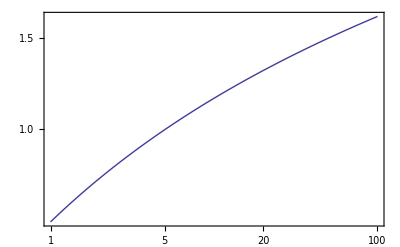

```mathematica
tr[k_]:=Log[1+2.34q]/(2.34q)(1+.85 q)/(1+q)(1+3.89q+(16.1q)^2+(5.46q)^2+(6.71q)^4)^(-.25)/.q->8k
dg[a_]:=a(1-.17 a^2)
δ[k_,a_]:=1300 k^2 tr[k]dg[a]
LogLogPlot[δ[k,.2],{k,1,100},Frame->True]
```

#### Hubble

```mathematica
Clear[h,v]
h[a_]:=70(.75+.25 a^-3)^(.5)
v[a_,k_]:=h[a]a/k
v[.1,500]
```

0.221691

#### Shock Acceleration

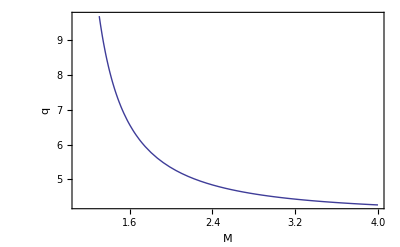

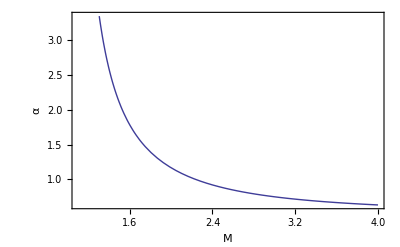

```mathematica
Plot[(4 m^2)/(m^2-1),{m,1.1,4},Frame->True,FrameLabel->{"M","q"},RotateLabel->False]
Plot[(m^2+3)/(2(m^2-1)),{m,1.1,4},Frame->True,FrameLabel->{"M","α"},RotateLabel->False]
```

4. Dark Energy

## 4.1 The Case for Dark Energy

### Observations

At the most fundamental level, the observations of the CMB have confirmed that the universe is flat to about 0.02 implying that Ω=1-Ω_Λ. X-ray observations of clusters imply that Ω=0.29. Relative distances to SNIa imply that H_0 d

```mathematica
df[a_,Ω_,ΩΛ_]:=NIntegrate[dh/(ap √(Ω/ap+ΩΛ ap^2)),{ap,a,1}]
dfplt=ContourPlot[5 Log[10,df[0.5,Ω,ΩΛ]/df[0.99,Ω,ΩΛ]],{Ω,0.01,1},{ΩΛ,0.01,1},Frame->True,Contours->{8.5,8.6,8.7,8.8,8.9,9.,9.1,9.2,9.3,9.4,9.5,9.6,9.7,9.8,9.9},ContourShading->False,FrameLabel->{Style["\!\(\*SubscriptBox[\(Ω\), \(m\)]\)",FontFamily->"Courier",FontSize->18,FontWeight->"Bold"],Style["\!\(\*SubscriptBox[\(Ω\), \(Λ\)]\)",FontFamily->"Courier",FontSize->18,FontWeight->"Bold"],Style["Magnitude Contours,a=.5, Δm=0.1",FontFamily->"Courier",FontSize->20,FontWeight->"Bold"],""},RotateLabel->False,DisplayFunction->Identity];
cmbline=Graphics[Line[{{1,0},{0,1}}]]
xrayline=Graphics[Line[{{0.29,0},{0.29,1}}]]
labelcmb=Graphics[Text["CMB",{0.5,0.6}]]
labelxray=Graphics[Text["X-ray",{0.35,0.1}]]
Show[dfplt,cmbline,xrayline,labelcmb,labelxray,DisplayFunction->$DisplayFunction]
```

Very accurate measurements are necessary to make distinguish world models

## 4.2 The problem of dark energy

The default view is that we inhabit a flat, underdense universe with a spatially and temporally constant (vacuum, dark, cosmological) energy density of 6 x 10^-9 erg cm^-3. There are many interesting and no compelling reasons why this should be 123 orders of magnitude smaller than the Planck density. The simplest view observationally is that Einstein's reason for introducing a cosmological constant - that the equations naturally admitted this possibility - is worth testing in an unbiased way.

## 4.3 Elaborating Dark Energy

We need to parametrize departures from ΛCDM. There are many possibilities. We must look to the future,beyond the Planck and other CMB observatories. Let us suppose that: 1. Baryons, dark matter, photons and neutrinos are conserved, 
2. There are no detectable effects of dark energy at and before the epoch of recombination. 
3. Standard atomic and nuclear physics is correct so that our inferences about nucleosynthesis and acoustic oscillations are valid. 
4. We have a sufficiently accurate knowledge of conditions at recombination and now. If we do not, we will have to use one of our observational approaches to solve for unknown parameters, eg the Hubble constant. 
5. The universe is flat. This last is the easiest to relax.

### 5.3.1 Kinematics

AΛCDM cosmology has j=1. We can introduce a kinematic

### 5.3.2 Thermodynamics

### 5.3.3 Field Theory

### 5.3.4 Dynamics

## 4.4 Observational Approaches

### 5.4.1 SNIa

### 5.4.2 Baryon Oscillation

A direct tracer of the kinematic expansion of the Universe is provided by the measurement of the density fluctuations that are a vestigial relic of the first acoustic peak in the microwave background spectrum. The best claimed detection is by Eisenstein et al 2005 and uses a redshift sample of 50,000 luminous red galaxies from the Sloan Digital Sky Survey over 4000 sq. deg. out to a ~ 0.7 with ā ~ 0.75. The volume explored is v(.7) ~18 Gpc^3 and the typical distance is d(.75) ~1. 3 Gpc.

```mathematica
d[.75]
```

1.30122

Measurement of baryon oscillation feature in 2 pt correlation function by Eisenstein et al.

### 5.4.3 Weak Lensing

### 5.4.4 Cluster counting

### 5.4.5 Integrated Sachs-Wolfe Effect

5.Gravitational Lenses

## 5.1 Geometrical Optics

### 5.1.1 Fundamentals of Strong Lensing

The fundamental equation is defined by simple geometry
β = θ + α̂
where β is the 2D angular position of the source, θ is the image position and α̂ = d_ds/d_s,α̂is the reduced deflection angle with α =a_d^-1 d_d^-1∇ψthe true deflection and 
ψ =d_d d_s ψ̂/d_ds=2∫ds ϕ 
d_ds is the distance from the deflector to the source and d_s the source distance.
ψ̂ satisfies the Poisson equation
∇^2 ψ̂=(8 πGa_d d_d d_ds)/d_sΣ=2 Σ/Σ_c,
where Σ is the surface density. and Σ_c =0.35(1 Gpc d_s/a_d d_d d_ds) g cm^-2 is the critical density.
The Greens function solution is 
ψ̂=∫dθ'ln|θ-θ'|(Σ/πΣ_c)
The associated time delay is 
t=(d_s(d_d(θ-β))^2)/(2 d_ds)-ψ
Introduce 
τ=θ^2/2-ψ̂
The Hessian is 
H_ij=β_(i,j)=τ_(,ij)=δ_ij+(ψ̂)_(,ij)=(1-κ-γ_1 | -γ_2
-γ_2 | 1-κ+γ_1)
where κ is the convergence and γ=(γ_1,γ_2)  is the shear.The magnification matrix is μ_ij=H_ij^-1, while the magnification is μ=[(1-κ)^2-γ^2]^-1. Critical curves are sky contours of infinite magnification where 1-κ = ±γ. Caustics are the corresponding curves in the source plane.
For a circular-symmetric lens,
μ=dθ^2/dβ^2

### 5.1.2 Fermat's Principle

t is stationary wrt to θ variations at true images (Fermat's principle).

```mathematica
u=0.1;v=0.1;
τ[x_,y_]:=0.5 (x^2+y^2)-4 (1+(x-u)^2+0.9 (y-v)^2)^0.5
ContourPlot[τ[x,y],{x,-5,5},{y,-5,5},Contours->100]
```

The images are located at extrema - maxima, minima and saddles. The inverse magnification contours exhibit the critical curve or Einstein ring

```mathematica
H[x_,y_]:=D[τ[x1,y1], x1,x1] D[τ[x1,y1], y1,y1]-(D[τ[x1,y1], x1,y1])^2/.{x1->x,y1->y}
ContourPlot[H[x,y],{x,-5,5},{y,-5,5},Contours->{-0.1,0,0.1}]
```

## 5.2Cosmography

Gravitational lenses contribute to measuring the size and shape of the universe in two important ways. They provide one of the best ways to measure the Hubble constant. The time delay for the variation between two images is t(θ_1)-t(θ_2) and measures H_0 if one knows ψ. Modeling is the challenge. The time delay has been measured well in several cases.

### 5.2.1 Hubble constant - B1608+656

#### Imaging

Imaged in radio, optical and infrared

#### Lens model

#### Radio time delays

#### Hubble Constant

h=0.75±0.07. However, generic systematic error of mass sheet looking like converging lens. There are complications associated with having an inhomogeneous universe which creates Poissonian contributions to the convergence and shear along the line of sight.

## 5.3 Dark Matter

### 5.3.1 Clusters Abell 1689

When one knows the redshifts of the arcs, it is possible to make a detailed model of mass distribution. In pricinciple, it is also possible to invert this procedure and constrain the density of dark matter and dark energy.

### 5.3.2 Galaxies

Consider an isothermal sphere. The equation of hydrostatic equilibrium is 
(d(ρσ^2))/dr=-ρg
where ρ∝r^-2 and g=4πρr. Hence Σ=σ^2/2b and α=4πσ^2. The Einstein radius is 
θ_E=(4 πσ^2 d_ds)/d_s=(σ/(190 km s^-1))^2(d_ds/d_s)arc sec
Gravitational lenses tell you about the density of dark matter in the inner parts of the galaxy, spectroscopy about the distributions at large radius.  This confirms that the total mass distribution is roughly isothermal, ie M~r.

Gravtitational lens in the HDF.

### 5.3.3 Stars -Microlensing

For point mass, α=4M/b, so the Einstein radius is
θ_E=((4 Md_ds)/(a_d d_d d_s))^(1/2)=0.1(M/M_o)^(1/2)((1pc d_ds)/(a_d d_d d_s))^(1/2)arc sec.
Typically this is unresolved.
In units of θ_E, the locations of the two images satisfy
θ^2-θβ-1=0

```mathematica
θp=θ/.Solve[θ^2-θ β-1==0,θ][[2]]
θm=-θ/.Solve[θ^2-θ β-1==0,θ][[1]]
μp= Simplify[(θp D[θp,β])/β]
Series[μp/.β->1/x,{x,0,4}]
μm= Simplify[(θm D[θm,β])/β]
Series[μm/.β->1/x,{x,0,4}]
μ=Simplify[μp-μm]
rat=Simplify[-μp/μm]
Solve[r==rat,β]
```

1/2 (β+√(4+β^2))

1/2 (-β+√(4+β^2))

((β+√(4+β^2))^2)/(4 β √(4+β^2))

1+x^4+O[x]^5

-((β-√(4+β^2))^2)/(4 β √(4+β^2))

-x^4+O[x]^5

(2+β^2)/(β √(4+β^2))

((β+√(4+β^2))^2)/((β-√(4+β^2))^2)

{{}}

```mathematica
Integrate[Sqrt[x(1-x)],{x,0,1}]
```

π/8

Using μ=(∂y^2)/(∂x^2),the total magnification is
μ_+-μ_-=(1+β^2/2)/((β(1+β^2/4))^(1/2))
Note that, if we denote R=-μ_+/μ_-, then θ_±=R^(±1/4).
We can plot the magnification curve as a function of time t for a star passing with unit speed in the lens plane and impact parameter b (in units of the Einstein radius).

```mathematica
M[t_,b_]:=(1+0.5 β^2)/(β (1+0.25 β^2)^0.5)/.β->√(b^2+t^2)
Plot[{M[t,1],M[t,0.5],M[t,0.2]},{t,-5,5},Frame->True,PlotRange->{1,6},FrameLabel->{Style["t",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"],Style["M",FontFamily->"Courier",FontSize->14,FontWeight->"Bold"]},ImageSize->600]
```

The optical depth of the Galaxy to microlensing is τ~πnR^3θ_E^2~4 πσ^2 f_* ~10^-6. Many such events have been observed and it has been possible to show that halo dark matter is not mostly compact objects. However a minor population of half solar masses lenses remains unexplained. There are also a few possible black hole candidates.